```mathematica
δa[r_]=(E^(-r^2/(2 a^2)))/((2π)^(3/2)a^3);α=0.1;u0=10^-20;δstart=10^-10;m=10;αSch=2m;ee={10^-10,10^-5,0.001,0.003,0.007,0.01,0.03,0.07,0.1,0.3,0.7,1};
Vs1[r_,a_,c1_]=- α/r Erf[r/(√2 a)]+c1 a^2 δa[r];
Vs2[r_,a_,{c2_,d1_}]=- 1/# Erf[#/(√2 a)]+c2 a^2 δa[#]+d1 a^4 Laplacian[δa[#],{#,θ,ϕ},"Spherical"]&[r];V[r_]=-α/r;
```

```mathematica
RS[n_,r_]=2/(A^(3/2) n^(3/2)) ⅇ^(-r/(n A)) Hypergeometric1F1[1-n,2,(2 r)/(n A)]/.A->Rationalize@(1/(m α));
```

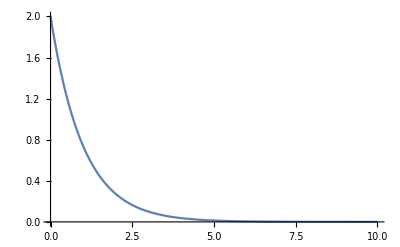

```mathematica
Plot[RS[1,r],{r,0,10},AxesOrigin->{0,0},PlotRange->Full]
```

```mathematica
a=0.1;c1=-0.69202747389763147321779640552930167553996396370027754885553564596947153122297`50.;
```

```mathematica
EigenEnergy[V_,αSch_,{min_,max_},{opt1___},{opt2___}]:=
Module[{sol,ef,evShifted,evnew,steps=∞,time1,time2},
PrintTemporary[V];
(*Module[{shift=10,d=1000,n=20,ev},{ev,ef}=NDEigensystem[{shift f[r]+V f[r]-1/αSch f''[r](*+NeumannValue[0,r==d]*),DirichletCondition[f[r]==0,True]},f[r],{r,0,d},n,Method->{"SpatialDiscretization"->{"FiniteElement",{"MeshOptions"->{"MaxCellMeasure"->0.05}}},"Eigensystem"->{"Arnoldi",MaxIterations->Infinity}}];
evShifted=ev-shift];
Print[evShifted];*)
sol=ParametricNDSolve[{V u[r]-1/αSch u''[r]==e u[r],u'[max]==-min,u[max]==min},u,{r,min,max},e,MaxSteps->steps,opt1];
evnew=e/.#&/@
Table[
PrintTemporary[n];FindRoot[u[e][min]==0/.sol,{e,0.99 SetPrecision[#[[n]],3],1.01 SetPrecision[#[[n]],3]}&[Table20REE],opt2(*,StepMonitor:>PrintTemporary[e]*)],{n,20}]
]
δ50e[en_,V_]:=Module[{sol,δs,δr,r1=50,r2=u0,β,jder,nder,k,wpc=50,prc=20,time1,time2},
time1=SessionTime[];
k=√(2en);
β:=r1 u'[r1]/u[r1]-1;
jder[r_]=D[SphericalBesselJ[0,r],r];
nder[r_]=D[SphericalBesselY[0,r],r];sol=Flatten@NDSolve[{u''[r]+αSch(en-V)u[r]==0,u'[r2]==1,u[r2]==u0},u,{r,r1,r2},PrecisionGoal->prc,WorkingPrecision->wpc, MaxSteps->Infinity,InterpolationOrder->All,Method->{"Shooting","StartingInitialConditions"->{u[r2]==u0,u'[r2]==1}}(*,SolveDelayed->True*)];
δs=FindRoot[(*u'[r1]/u[r1]==k Cot[k r1+δ]*)Tan[δ]==(k r1 jder[k r1]-β SphericalBesselJ[0,k r1])/(k r1 nder[k r1]-β SphericalBesselY[0,k r1])/.sol,{δ,0},WorkingPrecision->wpc,PrecisionGoal->prc];
δr=δ/.δs;
time2=SessionTime[];
Print["End with "<>ToString[time2-time1]<>"s"];
δr=NestWhile[Sign[#](Abs[#]-π)&,δr,Abs[#]>π/2&]
]
δ50[V_]:=Module[{en,len,δen,timestampa,timestampb},
len=Length@ee;
ParallelTable[
timestampa=SessionTime[];
en=ee[[i]];
δen=δ50e[en,V];
timestampb=SessionTime[];
Print[{en,δen},"    ",timestampb-timestampa];
δen,{i,2,len}]
]
Eigenfun[V_,enelist_]:=Module[{},Flatten[With[{r1=2000,r2=1.*10^-50},NDSolve[{V f[r]-1/αSch f''[r]==# f[r],f[r1]==r2,f'[r1]==-r2},f,{r,r1,r2},WorkingPrecision->50,AccuracyGoal->30,PrecisionGoal->15,InterpolationOrder->All,MaxSteps->Infinity,MaxStepSize->0.01,Method->{"Shooting","StartingInitialConditions"->{f'[r2]==1,f[r2]==r2}}]]&/@enelist,2]]
```

```mathematica
RealEigenEnergy[n_]=-(m α^2)/(2 n^2);
Table20REE=Table[RealEigenEnergy[n],{n,30}]
```

{-0.05,-0.0125,-0.00555556,-0.003125,-0.002,-0.00138889,-0.00102041,-0.00078125,-0.000617284,-0.0005,-0.000413223,-0.000347222,-0.000295858,-0.000255102,-0.000222222,-0.000195313,-0.00017301,-0.000154321,-0.000138504,-0.000125,-0.000113379,-0.000103306,-0.000094518,-0.0000868056,-0.00008,-0.0000739645,-0.0000685871,-0.0000637755,-0.000059453,-0.0000555556}

```mathematica
Eigenfunsin[V_,ene_,rr_,{r1_,r2_},opt___]:=
Module[{efunction,amplitude},efunction=Flatten[NDSolve[{V f[r]-1/αSch f''[r]==ene f[r],f[r1]==r2,f'[r1]==-r2},f,{r,r1,r2},opt,Method->{"Shooting","StartingInitialConditions"->{f'[r2]==1,f[r2]==r2}}],2];
amplitude=NIntegrate[f[r]^2/.#,{r,r2,r1}]^-0.5&/@efunction;
amplitude f[rr]/.efunction
]
```

## Matrix element <p^4>

```mathematica
Get["C:\\Users\\ASUS\\Documents\\DataDump_Coulomb_7_energyVs1_2nd.mx"]
```

NDSolve::precw: The precision of the differential equation ({{-(0.1 f[r])/r-f''[r]/20==-0.000125 f[r],f[4000]==1.×10^-50,f'[4000]==-1.×10^-50},{},{},{},{}}) is less than WorkingPrecision (50.).

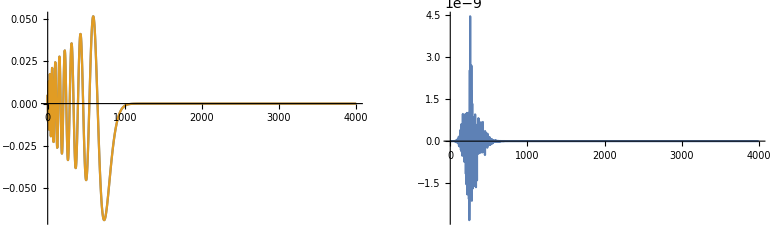
{3.5885,-Graphics-}

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in r near {r} = {8.44033×10^-26}. NIntegrate obtained 1.2446×10^17 and 1.28588×10^17 for the integral and error estimates.

1.2446×10^17

```mathematica
AbsoluteTiming@Module[{n=20},ef=First@Eigenfunsin[V[r],Table20REE[[n]],r,{4000,1.*10^-50},WorkingPrecision->50,PrecisionGoal->20,InterpolationOrder->All,MaxSteps->Infinity,MaxStepFraction->10^-4];ef=If[OddQ[n],ef,-ef];
GraphicsGrid@{{Plot[{ef,r RS[n,r]},{r,0,4000},PlotRange->Full,ImageSize->Medium],
Plot[{ef-r RS[n,r]},{r,0,4000},PlotRange->Full,ImageSize->Medium]}}
]
NIntegrate[D[ef,{r,2}]^2,{r,1.*10^-50,4000}]
```

```mathematica
NIntegrate[(D[ef,{r,2}])^2,{r,1.*10^-50,4000},Exclusions->50]-REAL[[20]]
```

-1.661×10^-16

```mathematica
N@REAL[[20]]
```

0.00098125

```mathematica
FalseVs1=Module[{efunction=Range@20},
ParallelTable[
efunction[[n]]=First@Eigenfunsin[V[r],Table20REE[[n]],r,{4000,1.*10^-50},WorkingPrecision->50,PrecisionGoal->15,InterpolationOrder->All,MaxSteps->Infinity,MaxStepFraction->10^-4];
NIntegrate[D[efunction[[n]],{r,2}]^2,{r,0,2000},Exclusions->True],{n,1,20}]
]
N[%,6]
Abs@((REAL-FalseVs1)/REAL);
N[%,6]
```

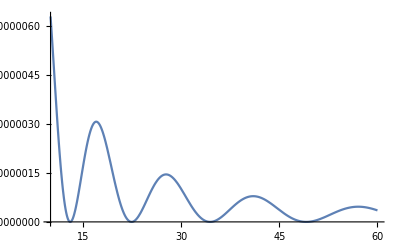

```mathematica
Plot[Evaluate@(D[ef,{r,2}]^2),{r,10,60},PlotRange->Full]
```

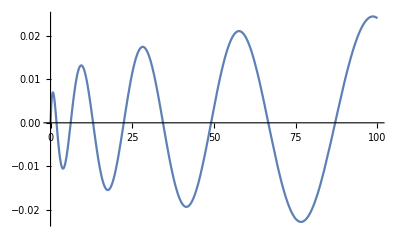

```mathematica
Plot[ef,{r,0,100}]
```

```mathematica
nRange=20;
```

```mathematica
p4Ture[n_,b_][Z_,γ_,η_,opt___]:=Z NIntegrate[(Laplacian[efVs2[[n]],{r}]^2),{r,0,b},opt]+γ/a NIntegrate[efVs2[[n]]^2 δa[r],{r,0,b},opt](*+η a NIntegrate[efVs2[[n]]^2 Laplacian[δa[r],{r,θ,ϕ},"Spherical"],{r,0,b},opt]*)
```

```mathematica
REAL=Table[Integrate[D[r RS[n,r],{r,2}]^2,{r,0,∞}],{n,nRange}];
REF=Table[Integrate[D[r RS[n,r],{r,2}]^2,{r,0,∞}],{n,nRange-2,nRange}];
```

### Matrix element in V_eff^(a^2)

```mathematica
efVs1=Module[{ef,am},
ef=Eigenfun[Vs1[r,a,c1],energyVs1];
am=NIntegrate[f[r]^2/.#,{r,1.*10^-50,2000}]^-0.5&/@ef;
(am[[2#]]=-am[[2#]])&@Range@10;
Table[am[[n]]f[r]/.ef[[n]],{n,20}]
]
```

NDSolve::precw: The precision of the differential equation ({{(-0.439393 Power[«2»]-0.1 Power[«2»] Erf[«1»]) f[r]-f''[r]/20==-0.0500078698243863935055737602971 f[r],f[2000]==1.×10^-50,f'[2000]==-1.×10^-50},{},{},{},{}}) is less than WorkingPrecision (50.).

NDSolve::precw: The precision of the differential equation ({{(-0.439393 Power[«2»]-0.1 Power[«2»] Erf[«1»]) f[r]-f''[r]/20==-0.0125002441801421361773951351802 f[r],f[2000]==1.×10^-50,f'[2000]==-1.×10^-50},{},{},{},{}}) is less than WorkingPrecision (50.).

NDSolve::precw: The precision of the differential equation ({{(-0.439393 Power[«2»]-0.1 Power[«2»] Erf[«1»]) f[r]-f''[r]/20==-0.00555558766918009791462567717346 f[r],f[2000]==1.×10^-50,f'[2000]==-1.×10^-50},{},{},{},{}}) is less than WorkingPrecision (50.).

General::stop: Further output of NDSolve::precw will be suppressed during this calculation.

$Aborted

```mathematica
DumpSave["C:\\Users\\ASUS\\Documents\\DataDump_Coulomb_7_efVs1_2nd.mx",efVs1]
```

```mathematica
AbsoluteTiming@GraphicsGrid@Partition[Table[Plot[{(RS[n,r]r),efVs1[r]},{r,0,2000},PlotRange->Full,ImageSize->Medium,PlotStyle->{Blue,Orange}],{n,20}],4]
AbsoluteTiming@GraphicsGrid@Partition[Table[Plot[(RS[n,r]r)-efVs1[r],{r,0,2000},PlotRange->Full,ImageSize->Medium],{n,20}],4]
```

```mathematica
FALSEVs1=NIntegrate[D[efVs1[[#]],{r,2}]^2,{r,0,2000},{MaxRecursion->30,WorkingPrecision->50,AccuracyGoal->30}]&/@Range@nRange
N[%,6]
Abs@((REAL-FALSEVs1)/REAL);
N[%,6]
```

```mathematica
RESVs1=FindRoot[Evaluate@Thread[(p4Ture[#,2000][Z,γ,η,{MaxRecursion->30,WorkingPrecision->50,AccuracyGoal->30}]&/@{10,15,20})==(REF[[#]]&/@{1,2,3})](*/.Z->1*),{{Z,1.1,1.12},{γ,0,100},{η,100,-2}},WorkingPrecision->50,AccuracyGoal->6,PrecisionGoal->6]
```

```mathematica
p4Vs1=p4Ture[#,2000][Z,γ,η,{MaxRecursion->30,WorkingPrecision->50,AccuracyGoal->30}]&/@Range@nRange/.RESVs1;
N[%,6]
Abs[(p4Vs1-REAL)/REAL];
N[%,6]
```

```mathematica
ef=Module[{efunction=Range@20},
SetSharedVariable[efunction];
ParallelTable[
efunction[[n]]=First@Eigenfunsin[V[r],Table20REE[[n]],r,{2000,1.*10^-50},WorkingPrecision->50,PrecisionGoal->15,InterpolationOrder->All,MaxSteps->Infinity,MaxStepFraction->10^-4];
ef=If[OddQ[n],ef,-ef],{n,1,15}];
ParallelTable[
efunction[[n]]=First@Eigenfunsin[V[r],Table20REE[[n]],r,{4000,1.*10^-50},WorkingPrecision->50,PrecisionGoal->15,InterpolationOrder->All,MaxSteps->Infinity,MaxStepFraction->10^-4];
ef=If[OddQ[n],ef,-ef];,{n,16,20}];
efunction
]
```

NDSolve::precw: The precision of the differential equation ({{-(0.1 f[r])/r-f''[r]/20==-0.05 f[r],f[2000]==1.×10^-50,f'[2000]==-1.×10^-50},{},{},{},{}}) is less than WorkingPrecision (50.).

NDSolve::precw: The precision of the differential equation ({{-(0.1 f[r])/r-f''[r]/20==-0.00555556 f[r],f[2000]==1.×10^-50,f'[2000]==-1.×10^-50},{},{},{},{}}) is less than WorkingPrecision (50.).

NDSolve::precw: The precision of the differential equation ({{-(0.1 f[r])/r-f''[r]/20==-0.002 f[r],f[2000]==1.×10^-50,f'[2000]==-1.×10^-50},{},{},{},{}}) is less than WorkingPrecision (50.).

NDSolve::precw: The precision of the differential equation ({{-(0.1 f[r])/r-f''[r]/20==-0.00102041 f[r],f[2000]==1.×10^-50,f'[2000]==-1.×10^-50},{},{},{},{}}) is less than WorkingPrecision (50.).